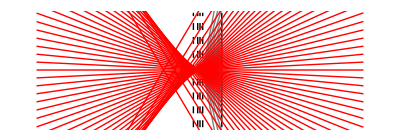

```mathematica
With[{ni=1.518,nm=1.33,dcs=5,θm=ArcSin[1.49/1.518],numθ=25,α=7.5,pry=15},Block[{θmlist,θilist,αnp},
θmlist=Join[Table[θ,{θ,-θm,-θm/numθ,θm/numθ}],Table[θ,{θ,θm/numθ,θm,θm/numθ}]];
θilist=ArcSin[nm/ni Sin[#]]&/@θmlist;
αnp=NIntegrate[(Tan[q]/Tan[ ArcSin[1.33/1.518Sin[q]]]),{q,0,ArcSin[1.4/1.52]}]/ArcSin[1.4/1.52];
Show[Graphics[{{{Thick,Line[{{0,-pry},{0,pry}}]},Dashed,Line[{{-dcs,-pry},{-dcs,pry}}],Line[{{-ni/nm dcs,-pry},{-ni/nm dcs,pry}}],Line[{{-(ni/nm)^3 dcs,-pry},{-(ni/nm)^3 dcs,pry}}],Line[{{-αnp dcs,-pry},{-αnp dcs,pry}}]},{Gray,Thin,Line[{{-dcs,0},{0,dcs Tan[#]}}]&/@θmlist},Thin,Red,Line[{{-(1+α)ni dcs/nm,0},{-(1-α)ni dcs/nm,0}}],Apply[Line[{{-(1+α)ni dcs/nm,dcs(Tan[#1]/Tan[#2]-(1-α)ni/nm)Tan[#2]-2α ni/nm dcs Tan[#2]},{-(1-α)ni dcs/nm,dcs(Tan[#1]/Tan[#2]-(1-α)ni/nm)Tan[#2]}}]&,Transpose[{θmlist,θilist}],2]}]
,PlotRange->{{-(1+α)ni dcs/nm,-(1-α)ni dcs/nm},{-pry,pry}}]]]
```

```mathematica
abeW[u_]:=
```

```mathematica
w20 [ni_,nm_][u_]:=(2ni)/nm (nm-ni)(1-√(1-u^2))/2
w40[ni_,nm_][u_]:=(2 ni^2)/nm^3 (nm^2-ni^2)((1-√(1-u^2))/2)^2
def[ni_,zf_][u_]:=ni zf √(1-u^2)
```

```mathematica
Sin[θ/2]^2//TrigExpand
```

Sin[θ/2]^2

```mathematica
NIntegrate[(Tan[q]/Tan[ ArcSin[1.33/1.518Sin[q]]]),{q,0,ArcSin[1.4/1.52]}]/ArcSin[1.4/1.52]-1
```

0.261176

```mathematica
1.518/1.33-1
```

0.141353

```mathematica
With[{ni=1.518,nm=1.33,dcs=5,θm=ArcSin[1.49/1.518],numθ=25,α=1.2,pry=2},
Manipulate[Plot[def[ni,zf][u]+w20 [ni,nm][u]+w40[ni,nm][u],{u,0,1.49/1.518}]
,{zf,-1,0}]]
```

```mathematica
D[def[ni,zf][u]+w20 [ni,nm][u]+w40[ni,nm][u],u]
```

(ni (-ni+nm) u)/(nm √(1-u^2))+(ni^2 (-ni^2+nm^2) u (1-√(1-u^2)))/(nm^3 √(1-u^2))-(ni u zf)/(√(1-u^2))

```mathematica
With[{ni=1.518,nm=1.33,dcs=5,θm=ArcSin[1.49/1.518],numθ=25,α=1.2,pry=2},
Manipulate[Plot[(ni (-ni+nm) u)/(nm √(1-u^2))+(ni^2 (-ni^2+nm^2) u (1-√(1-u^2)))/(nm^3 √(1-u^2))-(ni u zf)/(√(1-u^2)),{u,0,1.49/1.518}]
,{zf,-1,0}]]
```

```mathematica
With[{ni=1.518,nm=1.33,dcs=5,θm=ArcSin[1.49/1.518],numθ=25,pry=2},
Manipulate[Plot[{ni/nm √(1-(ni/nm u)^2)-α √(1-u^2),-(ni^3 u)/(nm^3 √(1-(ni^2 u^2)/nm^2))+(u α)/(√(1-u^2))},{u,0,nm/ni +0 1.49/1.518}]
,{α,1,2}]]
```

```mathematica
Integrate[ni/nm √(1-(ni/nm u)^2)-α √(1-u^2),{u,0,nm/ni}]
```

ConditionalExpression[1/4 (π-2 α ((nm √(1-nm^2/ni^2))/ni+ArcSin[nm/ni])), Re[ni/nm]>1||Re[ni/nm]<-1||ni/nm∉ℝ]

```mathematica
D[ni/nm √(1-(ni/nm u)^2)-α √(1-u^2),{u,1}]
```

-(ni^3 u)/(nm^3 √(1-(ni^2 u^2)/nm^2))+(u α)/(√(1-u^2))

```mathematica
With[{ni=1.518,nm=1.33},{ni/nm,ni^3/nm^3}]
```

{1.14135,1.48683}